# Trabalho Individual(Opcional) Lei de Coulomb

## Fundamentos de Física 3 - 2023/2 Aluno Caio Cordeiro Jácome

## Questão 2 - Dados 2 elétrons, cada um com carga elétrica −1, 60×10^-19C, separados por uma distância d = 0, 1nm, obtenha as forças Coulombianas entre eles, diagramando-as vetorialmente. - calcular numericamente via Wolfram Mathematica o módulo da força, F(d), entre os 2 elétrons, para os valores numéricos dados; - fazer via Wolfram Mathematica um gráfico do módulo da força, F(d) x d, variando d entre 0 nm e 1 nm, com título e nomes dos eixos.

#### Calculando numericamente o módulo das forças entre os elétrons q1, q2 e q3; Temos:

q_1=q_2= -1,60X 10^-19 C
d = 0,1nm 
k=8.99 X 10^-9  N·m^2/C^2= 1/(4πξ)
|F|= K  (q_1 X q_2)/r^2

2.30144×10^-8

Power::infy: Infinite expression 1/0 encountered.

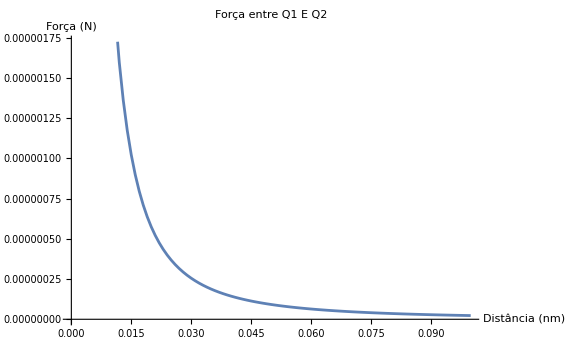

Syntax::tsntxi: "d=0,1*10^-9;" is incomplete; more input is needed.

```mathematica
k=8.99*10^9; 
q1=-1.60*10^-19; 
q2=-1.60*10^-19; 
d =1* 10^-10;
forca1 = (k*Abs[q1*q2])/(d^2);
Print[forca1]
distancias=Table[d,{d,0,1*10^-10,1*10^-12}];

forca=(k*Abs[q1*q2])/(distancias^2);
(*Cria o gráfico*)
ListLinePlot[Transpose[{distancias*10^9,forca}],
PlotLabel->"Força entre Q1 E Q2",
AxesLabel->{"Distância (nm)","Força (N)"},
FrameLabel->{"Distância (nm)","Módulo da Força (N)"}]
```